# Efficient Bayesian Regularization

Brian Beckman
December June 2023

## Abstract

The contributions here are to:

show numerical equivalence of three methods of linear regression: MAP (Maximum A-Posteriori), KAL (Kalman filtering/folding), and RLS (Recurrent Least Squares) when they are regularized by Bayesian a-priori beliefs, that is, protected from overfitting

remove risky matrix inversion from MAP, KAL, and RLS

remove expensive storage of observation vectors and matrices from MAP by rewriting MAP in recurrent form

show numerical equivalence of KAL to recurrent MAP when MAP’s regularization hyperparameters α=1/σ_ξ^2 and β=1/σ_ζ^2 are swapped and inverted

conjecture formal equivalence and support the conjecture algebraically through order three

sketch application of MAP, KAL, and RLS to Finite-Difference Policy Gradient in Reinforcement Learning

apply all methods to a non-linear Padé approximant

## Introduction

We investigate four popular methods for linear regression, i.e., parameter estimation, specifically with respect to the listed properties:

MLE — Maximum Likelihood Estimation

Is exposed to overfitting.

Stores and inverts large matrices.

Has numerical hazards of matrix inversion.

MAP — Maximum A-Posteriori

Addresses overfitting via regularization hyperparameters.

The standard algorithm stores and inverts large matrices.

When MAP’s hyperparameters are swapped and inverted, MAP’s recurrent form resembles KAL.

KAL — Kalman filtering

Addresses overfitting via frank priors: estimates and covariances.

Runs in constant memory. The recurrent form is standard.

Dual co-Kalman and co-RLS address Finite-Difference Policy Gradient in Reinforcement Learning.

RLS — Recurrent Least Squares

Matches KAL when renormalized by observation covariance.

Has apparently lower numerical risk than KAL.

Avoids subtraction in the covariance update.

We show that recurrent MAP, KAL, and RLS are numerically equivalent for appropriate choices of a-priori covariances. We conjecture that they’re mathematically equivalent and present analytical evidence for the conjecture.

We show how to apply MAP, KAL, and RLS to an important practical problem: Finite-Difference Policy Gradient in Reinforcement Learning.

We close with a new example: Padé approximants. Linearization opens them to KAL and RLS filtering.

## Overfitting and Regularization

Over-fitting is a hazard of linear regression. Linear models, as their number of parameters nears or exceeds the number of data points, follow the data too well — “wiggle too much.” Such wiggling limits the utility of predictions. Between data points and outside data ranges, predictions become unreliable. We show visual demonstrations below after setting things up.

Regularization is the usual fix for over-fitting. Bayesian MAP regularizes via a-priori belief hyperparameters α=1/σ_ξ^2 and β=1/σ_ζ^2 — reciprocal variances of the unknown parameters ξ and the noise on observations ζ. MAP does not include prior estimates for the parameters ξ themselves.

Kalman filtering (KAL) and recurrent least squares (RLS) are structurally superior because they incorporate priors as extra observations with covariances. KAL and RLS can be stopped and restarted at any point in an infinite stream of observations, and do not need tuning.

RLS, renormalized with observation covariance, reproduces KAL and MAP within numerical errors. Renormalized RLS can have better numerical stability than KAL, trading off risk of ill-conditioning against risk of catastrophic cancelation.

We show below, algebraically through order three and numerically for orders higher than that, that MAP produces the same estimates as do KAL and renormalized RLS when α and β are swapped and inverted. After swapping and inverting α and β, the MAP equations resemble the equations of Kalman filtering, at least for the estimate. In post-processing, we un-swap and re-invert α and β to recover covariances from recurrent MAP.

MAP, KAL, and RLS all regularize, just in different ways.

KAL and RLS scale better than non-recurrent, full-storage MAP, which is a Bayesian modification of non-recurrent, full-storage MLE. There is no obvious way to convert MLE and MAP into recurrences, let alone to extend them to lazy sequences or asynchronous streams. KAL and RLS, however, are overtly recurrent. They are foldable: independent of the manner and means of data delivery. They avoid matrix storage, inversions, and multiplication.

## Motivating Example

We begin with MLE a familiar school example: estimate the slope m and intercept b of the best-fit line function z(x)=m x+b to noisy data (x_i,z_i).

Think of z(x)=m x+b, more generally; as a linear combination of potentially non-linear basis functions of x with coefficients m and b. In the expression z(x)=m x+b, there are two basis functions. The first is z_m(x)=x, the identity function of x. The linear combination m z_m(x)=m x happens, accidentally, to be linear in the independent variable x. Do not be distracted by that linearity; it is not the linearity we’re looking for. The linearity of m z_m(x)=m x in the parameter m is the interesting linearity. The second basis function, z_b(x)=1, is the constant 1, non-linear in x. The linear combination b z_b(x)=b×1=b is linear in the parameter b. Thus the entire linear combination z(x)=m z_m(x)+b z_b(x)=m x+b is linear in m and b, and all methods of estimating m and b are called linear regression.

The idea of linear combinations of non-linear functions extends to sophisticated models. A Fourier series ∑_(k=0)^∞ a_k e^(i ω_k x) is linear in the amplitudes a_k, but non-linear in the basis functions e^(i ω_k x). A linear combination of non-linear Bessel’s functions approximates a vibrating drumhead. A linear combination of non-linear spherical harmonics approximates a lumpy Earth or a Hydrogen atom. These examples emphasize that linear regression methods like MLE, MAP, KAL, and RLS pertain to sophisticated models, linear in the parameters but non-linear in the independent variables.

## MLE, Four Ways

We show numerical equivalence of four ways to do MLE:

(WBI) with Wolfram’s built-in functions

(CNE) directly through the classic normal equations

(LPI) via the Moore-Penrose left pseudoinverse

(SLS) sidestepping the (hazardous?) inverse by solving a linear system

Problem Statement

Find best-fitting parameters m (slope) and b (intercept), where z(x)=m x+b, given known, noisy data (z_1,z_2,…,z_k) and abscissae (x_1,x_2,…,x_k). Best-fitting means minimizing mean squared error.

Write this system as a matrix equation:

Ζ (observations; known, concrete, numerical; scalars in this example, but generalizable to vectors)

A (partials, Jacobian of the observation model z(x)=m x+b with respect to the unknown parameters Ξ=(m,b)ᵀ; rows containing values of basis functions (x_(i∈[1..k]),1); known, concrete, numerical)

Ξ=(m,b)ᵀ (model, aka state; unknown abstract, symbolic parameters to be estimated).

N rows of data Ζ and N rows of partials A come in matched pairs.

Ζ_(Ν×1)  =  (z_1
z_2
⋮
z_Ν)   =   (x_1 | 1
x_2 | 1
⋮ | ⋮
x_Ν | 1)  ·  (m_unknown
b_unknown)   +  noise   
=^def  A_(Ν×2)·Ξ_(2×1)  +  samples of NormalDistribution[0,σ_Ζ]

Ground Truth

Fake some data by (1) sampling a line specified by ground truth m_GT and b_GT, then (2) adding Gaussian observation noise. Run the faked data through the four estimation procedures WBI, CNE, LPI, SLS, and see how close the estimated m_estimated and b_estimated come to ground truth. This model is of order M=2. There are N=119 observed scalar data. Ζ is a column vector of dimension 119, a number picked arbitrarily.

In real-world applications, we rarely have ground truth. Its purpose here is to calibrate the four estimation procedures WBI, CNE, LPI, SLS.

Note and remember the ground-truth values m_GT=0.5, b_GT=-1/3.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials inhabit an N×M matrix A, an order-Ν column vector of order-Μ row-co-vectors. Each co-vector is the Jacobian gradient 1-form of A·Ξ with respect to Ξ, the vector of unknown parameters, evaluated at specific values of Ξ from the data. Leave partials as a global variable for the following demonstrations.

A major defect of MLE is that A and Z are large, potentially infinite, in row count. This defect is solved by recurrence, a major theme of this article.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},«115»,{2.9661,1.},{3.,1.}}

Faked Observations Ζ

Define a faking function and a global variable, data, for later use. Assume that the observations have unbiased (zero-mean) Gaussian white noise with variance σ_Ζ=0.65, a convenient but arbitrary value.

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseσ];
noiseσ=0.65;
data=fake[nData,noiseσ,partials,groundTruth];
Short[data,3]
```

{0.135592,«117»,1.15911}

Wolfram Built-In

The Wolfram built-in LinearModelFit computes an MLE for Ξ=(m
b). The results in the cell below should approximate ground truth reasonably well (the results are randomized every time the notebook is evaluated).

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,x,x];
Normal[model]
```

-0.377921+0.496463 x

Here is everything Wolfram has to say about this MLE (it’s a lot; use the notebook’s interactive buttons to expand and contract the display).

```mathematica
Association[(#->model[#])&/@model["Properties"]]
```

The most important attribute of the model is its covariance matrix. We come back to it below.

```mathematica
model["CovarianceMatrix"]//MatrixForm
```

(0.0062975 | -0.00267304
-0.00267304 | 0.00267304)

The following plot shows that Wolfram does a god job of estimating the parameters m and b. We have 119 data and two parameters to estimate, so overfitting is not because the number of data greatly exceeds the number of parameters. We’ll show overfitting soon enough.

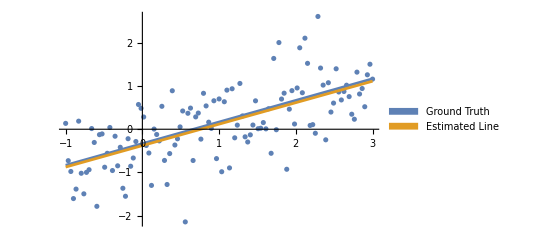

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m x+b,model[x]},{x,min,max},PlotLegends->SwatchLegend[{"Ground Truth","Estimated Line"}]]]
```

Normal Equations

Solve Equation 1 for a concrete value of Ξ that minimizes sum-squared error J(Ξ)=^def(Ζ-A·Ξ)ᵀ·(Ζ-A·Ξ) of the residuals (Ζ-A·Ξ). That is the same as maximizing the likelihood p ( Z|Ξ ) of the data Z given parameter values Ξ, giving MLE its name. Because the noise 𝒩(0,σ) is unbiased, the solution is exactly what one gets from naive algebra:  Aᵀ·A is square. When it is invertible:

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives numerically the same answer as Wolfram’s built-in, just in the opposite order:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
model["BestFitParameters"]
```

{0.496463,-0.377921}

{-0.377921,0.496463}

Moore-Penrose Left PseudoInverse

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it. We get exactly the same answer as above:

```mathematica
PseudoInverse[partials].data
```

{0.496463,-0.377921}

Avoiding Inverse

In general, we advise replacing any occurrence of Inverse[A].B  with LinearSolve[A,B]. See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/.

```mathematica
LinearSolve[partialsᵀ.partials,partialsᵀ].data
```

{0.496463,-0.377921}

## Do Not Use the Normal Equations

(Aᵀ·A)^-1·Aᵀ·Ζ is a nasty computation: big matrices, slow matrix multiplication, slow and numerically risky matrix inversion. How to avoid these hazards? Find a recurrence relation.

## Recurrence

## Recurrent Least Squares (RLS)

Derive, illustrate, and check a recurrent form of MLE. Regularize it (avoid overfitting) via Bayesian priors.

Fold the following recurrence over Ζ and A:

ξ←(Λ+[aᵀ·a])^-1·([aᵀ·ζ ]]+[Λ·ξ ]])
Λ←(Λ+[aᵀ·a])

where

ξ is the current estimate of Ξ, with prior ξ_0 for bootstrapping.

a and ζ are matched, concrete, numerical rows of partials A and observations Ζ, as in Equation 1.

Λ, with prior Λ_0, accumulates Aᵀ·A and implies the covariance matrix.

The priors ξ_0 and Λ_0 are the key to Bayesian regularization of RLS, as we shall see.

### Derivation Sketch

Derive the recurrence as follows: Treat the estimate-so-far, including the Bayesian prior ξ_0 as its first observation:

ξ_(so-far)=^def(A_(so-far)ᵀ·A_(so-far))^-1·A_(so-far)ᵀ·Ζ_(so-far)

Let Λ, the information matrix, be:

Λ=A_(so-far)ᵀ·A_(so-far)

with its prior, Λ_0.

The scalar performance or squared error of the known estimate, ξ_(so-far), is

J(ξ)  =  (Ζ_(so-far)-A_(so-far)·ξ)ᵀ·(Ζ_(so-far)-A_(so-far)·ξ)  =  (ξ-ξ_(so-far))ᵀ·Λ·(ξ-ξ_(so-far))

where

ξ is the unknown true parameter vector

Ζ_(so-far) is the known, concrete column vector of all observations so-far

Equation 6 obtains because Λ is symmetric and because Λ ξ_(so-far)=A_(so-far)Ζ_(so-far), from Equations 4 and 5.

Adding a new observation, ζ, and its corresponding partial row co-vector a, increases the error J(ξ) by (ζ-a·ξ)ᵀ·(ζ-a·ξ). Minimize the new total error with respect to the unknown ξ to find the recurrence (set the derivative of J with respect to ξ to zero and solve the resulting system). ■

RLS introduces an a-priori estimate ξ_0 and an a-priori information matrix Λ_0. RLS is therefore Bayesian by construction. When renormalized with an a-priori covariance for the observations ζ, the recurrence relation in Equation 3 is equivalent to KAL and numerically equivalent to MAP. We show the renormalization procedure in a later section. Rigorous proof of equivalence to MAP for all orders awaits future work, though Mathematica can prove it through order 3.

### Numerical Demonstration

Bootstrap the recurrence with ad-hoc, a-priori values ξ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)) — not much but just enough prior information. Update is foldable RLS. Avoid Inverse via LinearSolve.

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+ Λ.ξ)],Π}];

MatrixForm/@
({({{mBar}, {bBar}}),Π}=
Fold[update,
(* priors *)
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
(* sequence of observations and partials *)
{List/@data,List/@partials}ᵀ])
```

{(0.496463
-0.377921),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are, numerically, the same as we got from Wolfram’s built-in. For this example, the choice of ξ_0 and Λ_0 has negligible effect.

### Structural Notes

The highlighted mappings of List over the data and partials lists convert them from 1-dimensional puns of column vectors into 2-D column vectors.

### Memory and Time Efficiency

Because the observations and partial are the third argument of Fold, they need not be stored. They might as well be infinite and / or asynchronous streams. See https://community.wolfram.com/groups/-/m/t/3078712 and https://community.wolfram.com/groups/-/m/t/3074231.

The required memory for RLS is O (M^2), where M is the order of the model = the number of parameters to estimate = the length of Ξ = the length of each row of A, almost always small enough to fit in memory. The recurrence does not depend on the number N of data items.

RLS consumes O (M^3) time for LinearSolve at each step of the recurrence .

Contrast with the normal equations, which require O(N M) storage for A and Z and O(N M) time for Aᵀ.Z. N can be much larger than M or even M^2. N can even be infinite, making the normal equations impossible.

### Check the a-priori

The final value of Λ (called Π, a returned value), is A_full ᵀ·A_full+Λ_0. Check that the difference between Π and A_full ᵀ·A_full equals Λ_0, the a-priori covariance.

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

### Covariance of the Estimate

The covariance of this estimate Ξ is ((n-1)/(n-2))*Variance [ Ζ-A·Ξ ] except for a small contribution from the a-priori information Λ_0. The correction factor ((n-1)/(n-2)) is a generalization of Bessel’s correction. The 2 in (n-2) in the denominator is the number of parameters estimated, the degrees of freedom (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). In general, the denominator of the correction is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00267304 | -0.00267304
-0.00267304 | 0.0062975)

Check that this covariance approximately equals that deduced from Π, the final value of Λ:

```mathematica
(cov$=Inverse[Π]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}])//MatrixForm
```

(0.00267304 | -0.00267304
-0.00267304 | 0.0062975)

This is the same covariance matrix that Wolfram’s LinearModel reports. This second check of our recurrence succeeds.

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00267304 | -0.00267304
-0.00267304 | 0.0062975)

### Covariance of the Prediction

If we view the two parameters, m and b, as random variables, then the predicted value z at every input point x is a linear combination of random variables, thus a random variable. The following plot shows the one-sigma band around the predicted values.

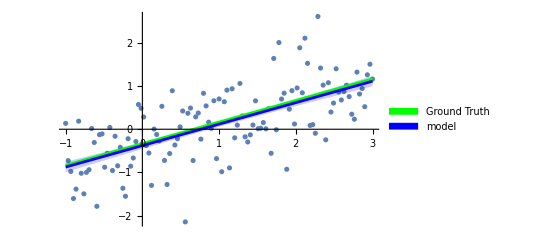

```mathematica
Module[{row,diagonalTerm,offDiagonalTerm,Σ},
row[x_]:={{x,1.}};
diagonalTerm[x_]:=Map[Dot[Diagonal[cov$],#]&,#^2&/@row[x]];
offDiagonalTerm[x_]:=MapThread[Dot,{row[x].cov$,row[x]}];
Σ[x_]:=Sqrt[(row[x].cov$.row[x]ᵀ)⟦1,1⟧];
With[{points={partials⟦All,1⟧,data}ᵀ},
Show[ListPlot[{points}],
Plot[{m x+b,
model[x],
model[x]+Σ[x],
model[x]-Σ[x]},{x,min,max},
PlotStyle->{
Green,Blue,
{Thin,{Opacity[0],Blue}},
{Thin,{Opacity[0],Blue}}},
Filling->{2->{3},2->{4}},PlotLegends->SwatchLegend[{"Ground Truth","model"}]]]]]
```

## Interim Conclusions

We have (notionally) eliminated O (N M) memory bloat by processing updates one observation at a time, each with its paired partial. When N exceeds memory or is infinite, this elimination is essential. The resulting forms are O(M) in storage, where M is the order of the model, almost always small enough to store in memory. The JPL Horizon project has a model with some 1.5 million parameters, for instance, still easy to fit in memory.

We reduce numerical risk by solving a linear system instead of inverting a matrix.

We avoid multiplication of O (N M) matrices, which may infeasible.

We still have work to do with renormalization and observation covariances.

## Regularization and Renormalization

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example of fitting polynomials starting in section 1.1. The higher the order of the polynomial, the more MLE over-fits. Bishop presents MAP regularization as a cure for this over-fitting. KAL and RLS regularize by construction. In this section, we relate KAL and RLS regularization by frank priors to Bishop’s MAP regularization by hyperparameters.

To bootstrap recurrences, KAL and RLS require a-priori estimates of the unknown parameters and their uncertainties. RLS takes the a-priori uncertainty of parameters as an information matrix; KAL takes it as a covariance matrix, inverse of the information matrix. Bishop also computes the information matrix as S^-1, though he does not name it so. KAL additionally requires an a-priori estimate of observation noise. We show how to renormalize RLS with observation noise to produce results equivalent to KAL and MAP.

Reproducing Bishop’s Example

### Bishop’s Training Set

First, create a sequence of Ν=10 inputs, equally spaced in [0,1].

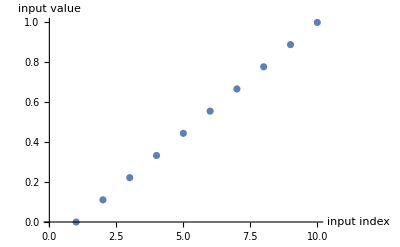

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
ListPlot[bishopTrainingSetX[10],AxesLabel->{"input index","input value"}]
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample of that ground truth taken at the inputs above. Bishop doesn’t state his observation noise, but I’ve reverse engineered σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the name bts for bishopTrainingSet. It is not his actual training set, which I did not find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

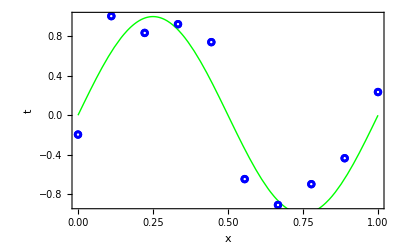

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

### Partials: Gradients of the Unknown Parameters

Write a function for partials. Quietly map the indeterminate 0^0 to 1. Test it symbolically.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
MatrixForm@partialsFn[6,{Subscript[x, 1],Subscript[x, 2],Subscript[x, Μ]}]
```

(1 | x_1 | x_1^2 | x_1^3 | x_1^4 | x_1^5 | x_1^6
1 | x_2 | x_2^2 | x_2^3 | x_2^4 | x_2^5 | x_2^6
1 | x_Μ | x_Μ^2 | x_Μ^3 | x_Μ^4 | x_Μ^5 | x_Μ^6)

### The Observation Equations

Confer Bishop’s Equation 3.3, page 138. He writes the parameters-to-estimate as w and he writes the observation equation as

y(x, w)=∑_(j=0)^Μ w_j ϕ_j (x)

(bias is the coefficient w_0 of the 0^th basis function). This is predictive: you give me concrete inputs x and parameters w, and I’ll give you a predicted observation y in terms of the Μ+1 basis functions ϕ corresponding to the Μ+1 unknown parameters w. The basis functions need not be polynomials. They can be anything: wavelets, Fourier waves, Chebyshev polynomials, etc.

Bishop transposes w into a co-vector and writes

y(x, w)=wᵀϕ (x)

where ϕ (x) is an (Μ+1)-dimensional column-vector of basis functions, each a transpose of one row of our partials matrix A. We prefer always to think of partials or gradients as co-vectors. See https://en.wikipedia.org/wiki/Covariance_and_contravariance _of _vectors, https://math.stackexchange.com/questions/1172022, and https://math.stackexchange.com/questions/54355). 

To find best-fit values for w, rows of the partials matrix A are the co-vector gradients of y with respect to w. We prefer to write

observations as height-N column-vector Ζ_Ν with elements ζ_(j ∈ [ 1 ..Ν ])

the model or unknown parameters, an (Μ+1)-dimensional column-vector Ξ_((Μ+1)×1) with elements ξ_(i ∈ [ 0 ..Μ ]) (here, ξ_0 is not a vector prior, but a bias term)

partials matrix as A_(N×(Μ+1))

Bishop calls our partials matrix the design matrix in his Equation 3.16, page 142, consisting of values of the basis functions at the concrete inputs x_(n ∈ [1..N]). Bishop works in the dual of our formulation, that is, already set up for finite-difference policy-gradient estimation.

Our KAL and RLS express co-vector rows of the design matrix as polynomial basis functions evaluated at the input points x_(n ∈ [1..Ν]):

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (1=x_1^0 | x_1 | x_1^2 | ⋯ | x_1^M
1=x_2^0 | x_2 | x_2^2 | ⋯ | x_2^M
⋮ | ⋮ |   | ⋱ | ⋮
1=x_N^0 | x_N | x_N^2 | ⋯ | x_N^M)  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

then packed up into rows of the A matrix.

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (A_(1×(Μ+1))(x_1)
A_(1×(Μ+1))(x_2)
⋮
A_(1×(Μ+1))(x_Ν))_(Ν×(Μ+1))  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

### MLE: The Normal Equations

For comparison purposes, mechanize the normal equations. Expect them to over-fit.

```mathematica
ClearAll[mleFit];
mleFit[Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
PseudoInverse[partialsFn[Μ,xs]].ys];
mleFit[3,bts]
```

{-0.120734,11.9417,-34.8694,23.4146}

The normal equations as a symbolic polynomial on bts follows. Notice we can increase the order beyond the number of data, creating an underdetermined system. Underdetermined systems are not typical in real-world data processing. Usually the number of data exceed the order and the system is overdetermined. The pseudoinverse in mleFit is agnostic to the distinction.

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
ClearAll[x];
Manipulate[
symbolicPowers[x,Μ].mleFit[Μ,bts],
{{Μ,3,"polynomial order Μ"},0,16,1,Appearance->{"Labeled"}}]
```

### RLS: Recurrent Least Squares

Regularize RLS by its a-priori estimate of the unknown parameters and by its a-priori information matrix. Slide the slider in the display below to decrease the incoming σ^2 of the information matrix by orders of magnitude. Check that, once the info becomes too small, the Λ matrix becomes ill-conditioned: pink warning message appear from the Wolfram kernel, and the solution becomes numerically suspect. In the rest of this paper, we eliminate these error message by applying Wolfram’s Quiet because we notice, empirically, that ill-conditioning of the information matrix does not seem harmful for this example. However, ill-conditioning is a problem in practice and must be tracked and managed with methods out-of-scope in this paper.

#### Non-Renormalized RLS Fitting Procedure

```mathematica
ClearAll[rlsFit];
rlsFit[σ2Λ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2Λ*IdentityMatrix[Μ+1]},
Fold[update,{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ]]];

Manipulate[
Column[{"10^-logσ2Λ"->10^-logσ2Λ,
"fit Bishop's data"->(rlsFit[10^-logσ2Λ][3,bts]⟦1⟧//MatrixForm)}],
{{logσ2Λ,9.034},0,16,Appearance->"Labeled"}]
```

### KAL: Foldable Kalman Filter

The foldable Kalman filter (KAL) follows below. This version has only the update phase of a typical Kalman filter because the parameters-to-estimate are constant and therefore there is no predict phase.

Note the P_Ζ parameter, the first in the definition of kalmanUpdate. This is the covariance matrix of the observation noise. It is a constant throughout the folding run of the filter. That is why we lambda-lift P_Ζ into its own function slot. kalmanUpdate, given some concrete value of P_Ζ=σ_ζ^2 ℐ, yields a foldable function of {current state,covariance} and of {new data,partials}. Initialize the fold in kalFit with a-priori estimate ξ_0=0 and covariance P_0=σ_ξ^2 ℐ, and run the fold over observation-and-partial pairs {ζ,a}.

### Kalman Fitting Procedure

```mathematica
ClearAll[kalmanUpdate,kalFit];
kalmanUpdate[PΖ_][{ξ_,P_},{ζ_,a_}]:=
Module[{D,KT,K,L},
D=PΖ+a.P.aᵀ;
KT=LinearSolve[D,a.P];K=KTᵀ;
L=IdentityMatrix[Length[P]]-K.a;
{ξ+K.(ζ-a.ξ),L.P}];

kalFit[σζ2_,σξ2_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,order+1],
P0=σξ2*IdentityMatrix[order+1]},
Fold[kalmanUpdate[σζ2*IdentityMatrix[1]],
{ξ0,P0},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
```

### See All Three

The following interactive demonstration shows mleFit (normal equations), rlsFit (non-renormalized recurrent least squares), and kalFit (Kalman folding) on Bishop’s training set.

On a 9^th-order polynomial, both KAL and RLS regularize when the a-priori information is 10^-6 ℐ and the a-priori covariance is 10^6 ℐ. In contrast, the MLE over-fits a by running through every data point. A 9^th-order polynomial fits the M+1=10 data points of the example exactly.

Increasing -logΛ decreases a-priori information in RLS, decreasing belief in the a-priori ξ_0. Increasing logσξ2 increases the a-priori covariance σ_ξ_0^2 of ξ_0, also decreasing belief in ξ_0. As σ_ξ_0^2 increases, RLS and KAL eventually over-fit and align with MLE. Later, we show that MAP similarly over-fits as belief in ξ_0 decreases.

Run the polynomial order up to nine, then run -logΛ and logσξ2 all the way to the right, to their maximum values, to see overfitting, that is, failure of regularization.

The Green line is Ground Truth.

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{
recurrent=Quiet@rlsFit[10^-logΛ0][Μ,bts],
normal=mleFit[Μ,bts],
kalman=kalFit[bishopFakeSigma^2,10^logσξ2][Μ,bts]},
With[{
rlsFn={terms}.recurrent⟦1⟧,
mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{
{Grid[{{
Button["RESET",(Μ=9;logΛ0=3;logσξ2=3)&],
Control[{{rlsQ,True,Style["RLS",Bold,Purple]},{True,False}}],
Control[{{kalQ,True,Style["KAL",Bold,Cyan]},{True,False}}],
Control[{{mleQ,True,Style["MLE",Bold,Orange]},{True,False}}]}}]},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logΛ0,3,"-log a-priori info (RLS)"},0,16,Appearance->"Labeled"}]},{Control[{{logσξ2,3,"log a-priori cov (KAL)"},0,16,Appearance->"Labeled"}]}}]]
```

Renormalizing RLS

When the observation noise Ζ is unity, KAL coincides with RLS. In the demonstration below, a-priori information Λ in RLS is set always to be the inverse of KAL’s a-priori covariance P. KAL and RLS will have the same belief in the a-priori parameters ξ_0. Vary the observation noise independently to see KAL and RLS coincide when the observation noise is unity (its log is zero).

As observation noise decreases, the solutions believe the observations more than the a-prioris and RLS and KAL over-fit. As a-priori covariance decreases, RLS and KAL believe the a-prioris more than the observations and the solution regularizes.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{rls=Quiet@rlsFit[10^(-2logσξ)][Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{rlsFn={terms}.rls⟦1⟧,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(logσζ=0.0;logσξ=1.5;Μ=9)&],
Control[{{rlsQ,True,Style["RLS",Bold,Purple]},{True,False}}],
Control[{{kalQ,True,Style["KAL",Bold,Cyan]},{True,False}}]}}],""},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}],""},{Control[{{logσξ,1.5,"log √P (KAL) = (-log √Λ) (RLS) "},-3,8,Appearance->"Labeled"}]},{Control[{{logσζ,0.0,"log √Ζ (KAL)"},-6,3,Appearance->"Labeled"}]}}]]
```

### Renormalized RLS

RLS, so far, is normalized to unit observation noise. How to modify RLS to account for non-unit observation noise?

Scale (each row of) the partials by 1/σ_z the inverse of the observation standard deviation σ_z. Rescale the final estimate (not the final covariance) by a matrix built from 1/σ_z because the recurrent normal equation, (P_Ζ^-1 AᵀA P_Ζ^-T)^-1 P_Ζ^-1 AᵀΖ, has one too many factors of P_Ζ.

Redefine rlsUpdate to include this renormalization and notice that it’s always equal to KAL.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];

Manipulate[
With[{ξ0=({{0}, {0}}),Λ0=({{1.0*^-6, 0}, {0, 1.0*^-6}}),m=MatrixForm,
inputs={List/@data⟦1;;n⟧,List/@partials⟦1;;n⟧}ᵀ},
Module[{ξrr,ξr,ξk,Πrr,Πr,Πk},
({ξrr,Πrr}=Fold[rlsUpdate[σ IdentityMatrix[1]],
{ξ0,Λ0},inputs]);
({ξr,Πr}=Fold[update,{ξ0,Λ0},inputs]);
({ξk,Πk}=Fold[kalmanUpdate[σ^2],{ξ0,Inverse@Λ0},inputs]);
Grid[{
{"","Renormalized RLS","RLS","KAL"},
{"Estimate",m[(IdentityMatrix[2]/σ).ξrr],m@ξr,m@ξk},
{"Info Mat",m@Πrr,m[Πr/σ^2],m[Inverse@Πk]},
{"Mat Diffs",
m@Chop[Abs[Πrr-Πr/σ^2],10^-9],
m@Chop[Abs[Inverse@Πk-Πr/σ^2],10^-9],
m@Chop[Abs[Inverse@Πk-Πrr],10^-9]}},Frame->{All,{True,True,None}}]]],
{{n,3},3,nData,1,Appearance->"Labeled"},
{{σ,10},-100,100,Appearance->"Labeled"}]
```

### Renormalized RLS beats KAL

KAL and renormalized RLS are mathematically equivalent (stated withoutt proof). Operationally, KAL subtracts matrices to update estimated covariance. Subtraction is exposed to catastrophic cancelation. Renormalized RLS only adds to the information matrix, so is exposed only to ill-conditioning, which is empirically less severe than catastrophic cancelation. We show this below.

## Regularization and MAP

Bishop reports β=11.111… and α=0.005 in his figure 1.17 (page 32) and in his Equations 1.70 through 1.72 (page 31). These equations look suspiciously like the equations for Kalman filtering. Bishop’s matrix S looks like D^-1 in kalmanUpdate above. Let’s reproduce MAP via KAL and renormalized RLS.

Bishop’s MAP

### The MAP Equations

Bishop’s Equations 1.70 through 1.72 are reproduced here. The dimensions of the identity matrix in S are Μ+1, where Μ is the order of the polynomial model, one more than Μ to account for a bias term. It turns out that Bishop’s S^-1 is exactly the information matrix of RLS, as we see in the section on Covariance of the Prediction, below. Bishop’s hyperparameters, α=1/σ_ξ^2 and β=1/σ_ζ^2, are reciprocal variances of the a-priori estimates and the observations, respectively.

m(x)  =  β ϕ (x)ᵀ·S·∑_(n=1)^N ϕ (x_n)t_n

s^2(x)  =  β^-1+ϕ (x)ᵀ·S·ϕ (x)

S^-1  =^def  α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ

Here are some links between Bishop’s formulation and ours, without derivation.

∑_(n=1)^N ϕ (x_n)t_n=Aᵀ·Ζ

lim_(α→0) ( β^-1 S^-1)=Aᵀ·A

### Φ Vectors

Bishop’s ϕ (x_n) is an (Μ+1)-dimensional column vector of the powers of the n^th input x_n. These powers are the basis functions of a polynomial model for the curve. ϕ (x_n) is the dual of one row of our partials matrix A.

As written, Bishop’s equations are non-recurrent, requiring all data t_n and ϕ (x_n) in memory. Plus, as written, they require inverting matrix S. They thus suffer from all the operational ills of the normal equations: too much memory, too much time, and numerical risk.

```mathematica
ClearAll[ϕ];
ϕ[Μ_][xn_]:=Quiet@Table[xn^i,{i,0,Μ}]/.{Indeterminate->1};
MatrixForm/@ϕ[3]/@List/@bts⟦1⟧
```

{(1
0.
0.
0.),(1.
0.111111
0.0123457
0.00137174),(1.
0.222222
0.0493827
0.0109739),(1.
0.333333
0.111111
0.037037),(1.
0.444444
0.197531
0.0877915),(1.
0.555556
0.308642
0.171468),(1.
0.666667
0.444444
0.296296),(1.
0.777778
0.604938
0.470508),(1.
0.888889
0.790123
0.702332),(1.
1.
1.
1.)}

### S Inverse

Bishop’s Equation 1.72.

```mathematica
ClearAll[sInv,α,β];
sInv[α_,β_,cs_,Μ_]:=
With[{Ν=Length[cs]},
α IdentityMatrix[Μ+1]+β Sum[cs⟦i⟧.cs⟦i⟧ᵀ,{i,Ν}]];
```

### MAP Mean

Bishop’s Equation 1.70, replacing Inverse with LinearSolve as we usually do:

```mathematica
ClearAll[mapMean];
mapMean[α_,β_,x_,cs_,ts_,Μ_]:=
With[{Ν=Length@cs},
{β*ϕ[Μ][x]}.(* row of partials *)
LinearSolve[(* vector of coefficients *)
sInv[α,β,cs,Μ],
ts.cs]]⟦1,1⟧;
```

### a-priori Variances α and β

Bishop defines β=1/σ_ζ^2, where σ_ζ is the standard deviation of the observations ζ. The predicted observation ζ is the value of the model on an arbitrary input ξ. Similarly, Bishop defines α=1/σ_ξ^2, where σ_ξ is the standard deviation of the a-priori distribution of the unknown parameter estimate ξ.

#### Mean Is Invariant Under “Swap and Invert”

We observe, numerically and algebraically through order 3, that Bishop's equations for the estimate match KAL and RLS when the covariances are swapped and inverted, that is, when  β is σ_ξ^2 and when α=σ_ζ^2. The demonstration below shows symbolically that the estimates (not covariances) m1≡mapMean[α,β,x,cs,ts,Μ] and m2≡mapMean[1/β,1/α,x,cs,ts,M], are equal. Mathematica has trouble simplifying m1-m2, for orders 1 and 4. For order 1, visual inspection of m1 and m2 reveal approximate equality. For orders 4 and greater, we rely on the numerical check. For fun, we include symbolic forms for the information matrix, sInv[α,β,cs,M] and a nominal form sInv[1/β,1/α,cs,M]. We invite readers to perform rigorous analysis and even find a proof.

```mathematica
ClearAll[x,α,β,chopQ];
DynamicModule[{chopQ=True},
Manipulate[With[{cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,
pf=If[chopQ,Chop,Identity]@*FullSimplify},
With[{m1=mapMean[α,β,x,cs,ts,Μ],
m2=mapMean[1/β,1/α,x,cs,ts,Μ]},
Grid[({{"m1", pf@m1}, {"m2", pf@m2}, {"m1-m2", pf[m1-m2]}, {"N(m1-m2)", Plot3D[Log10[1+pf[m1-m2]],
{α,0,2.0},
{β,0,2.0}]}}),Frame->All]]],
Column[{Row[{Button["UN-CHOP",chopQ=False],"        ",
Button["CHOP",chopQ=True]}],
Control[{{Μ,2,"order Μ"},0,9,1,Appearance->{"Open","Labeled"}}]}]]]
```

## Numerical Equivalences

In the following demonstration, the numerical evidence for equality of the estimates (not equality of the covariances) produced by the two applications of MAP becomes overwhelming. MAP, RLS, and KAL match for all settings of σ_ξ^2, σ_ζ^2, M (order of the model), and assignments of α and β.

The one deviation from perfect match concerns KAL. Explore M=4. For high σ_ξ^2 (we do not believe the a-priori estimate of ξ) or low σ_ζ^2 (we do believe the observational data), KAL fluctuates wildly. Why? The Kalman denominator D=P_ζ+aᵀ P_ξ a becomes nearly aᵀ P_ξ a. The Kalman gain, K=P_ξ aᵀ D^-1 is nearly a^-1. The covariance update, (I-Ka)P, becomes ill-conditioned, if not negative, because Ka is near the identity. Other papers in this series mitigate this defect via alternative, mathematically equivalent, forms for P.

RLS does not suffer from these ills because it never subtracts. RLS is still exposed to ill-conditioning of the information matrix, but that seems numerically less harmful to the final result in this example.

Wrap RLS in Quiet to suppress warnings. There is no free lunch; MAP also shows ill-conditioning and is similarly wrapped.

### Recurrent RLS Fitting Procedure

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
DynamicModule[{αβBishop=True},
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[σζ2,σξ2][Μ,bts],
rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{α=If[αβBishop,1/σξ2,σζ2],β=If[αβBishop,1/σζ2,σξ2]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
mapFn=Quiet@mapMean[α,β,x,cs,ts,Μ],
rlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},(* green for ground truth *)
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
If[mapQ,AppendTo[showlist,Plot[mapFn,{x,0,1},PlotStyle->{Magenta}]]];
Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]]],
Column[{SetterBar[Dynamic[αβBishop],{True->"α = 1/σ_ξ^2, β = 1/σ_ζ^2",False->"α = σ_ζ^2, β = σ_ξ^2"}],
Row[{Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{kalQ,True,Style["        KAL",Bold,Cyan]},{True,False}}],
Control[{{rlsQ,True,Style["        RLS",Bold,Purple]},{True,False}}],
Control[{{mleQ,False,Style["        MLE",Bold,Orange]},{True,False}}],
Control[{{mapQ,True,Style["        MAP",Bold,Magenta]},{True,False}}]},Frame->All],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]]
```

#### Covariance and Information Matrices

Notice that Bishop' s S^-1 is different when α and β are swapped and inverted; it’s only an information matrix when α and β have their original assignments as 1/σ_ξ^2 and 1/σ_ζ^2, respectively. The meaning of S^-1 under the swapped and inverted assignments of α and β has not been explored.

```mathematica
DynamicModule[{αβBishop=True},
Manipulate[Module[{x},
With[{cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{kalman=kalFit[σζ2,σξ2][Μ,bts],
rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{α=If[αβBishop,1/σξ2,σζ2],β=If[αβBishop,1/σζ2,σξ2]},
Grid[({{"inverse\nKAL P", MatrixForm[Inverse[kalman⟦2⟧]]}, {"rrls Λ", MatrixForm[rrls⟦2⟧]}, {"Bishop S^-1", MatrixForm[sInv[α,β,cs,Μ]]}})]   ]]]],
Column[{SetterBar[Dynamic[αβBishop],{True->"α = 1/σ_ξ^2, β = 1/σ_ζ^2",False->"α = σ_ζ^2, β = σ_ξ^2"}],
Row[{Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&]},Frame->All],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]]
```

### Covariance of the Prediction

The following shows estimated coefficients with their error bars. To translate from covariance of the estimate to covariance of the prediction, observe that the prediction is a linear combination of the estimates. Following https://stats.stackexchange.com/questions/160230, the covariance of the prediction at each input x is a(x)P (a (x))ᵀ. Bishop adds the fixed observation covariance σ_ζ^2 to the covariance of the prediction.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{k=kalFit[σζ2,σξ2][Μ,bts]},
With[{δξ=Sqrt@Diagonal[k⟦2⟧],
ξ=Flatten@k⟦1⟧},
With[{eds={ξ,δξ}ᵀ},
Show[{ListPlot[Around/@eds,Joined->True]}]]]]]],
Column[{
Row[{Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

Consider Bishop' s Equation 1.71 s^2(x)=β^-1+ϕ (x)ᵀS ϕ (x), which does not depend on the output data t_n, just as with KAL and RLS.

```mathematica
ClearAll[mapsSquared];
mapsSquared[α_,β_,x_,cs_,Μ_]:=
With[{a=ϕ[Μ][x]},
β^-1+{a}.LinearSolve[sInv[α,β,cs,Μ],List/@a]];
```

Bishop kindly supplies the sigma-bars for his mean. He cites α=0.005 and β=11.1, which correspond to σ_ζ=0.07071 and σ_ξ=3.333, and log_10 σ_ζ=-1.15051 and log_10 σ_ξ=0.5229. These values reproduce Bishop’s Figure 1.17 well. Bishop’s Equation 1.71 equals σ_ζ^2+a_row(x)·P·a_row(x)ᵀ.

```mathematica
Manipulate[Module[{x,Σ2Fn},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σ2ξ=10^(2logσξ),σ2ζ=10^(2logσζ)},
With[{kalman=kalFit[σ2ζ,σ2ξ][Μ,bts]},
With[{kalFn={terms}.kalman⟦1⟧,
bs2=mapsSquared[1/σ2ξ,1/σ2ζ,x,cs,Μ],
mapFn=Quiet@mapMean[σ2ζ,σ2ξ,x,cs,ts,Μ]},
Σ2Fn=σ2ζ+({terms}.kalman⟦2⟧.{terms}ᵀ)⟦1⟧;
With[{lp=ListPlot[btsᵀ,PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[kalQ,AppendTo[showlist,
Plot[{kalFn,kalFn+√Σ2Fn,kalFn-√Σ2Fn},{x,0,1},
PlotStyle->{Cyan,{Thin,{Opacity[0],Cyan}},{Thin,{Opacity[0],Cyan}}},Filling->{1->{2},1->{3}}]]];
If[mapQ,AppendTo[showlist,
Plot[{mapFn,mapFn+√bs2,mapFn-√bs2},{x,0,1},
PlotStyle->{Magenta,{Thin,{Opacity[0],Magenta}},{Thin,{Opacity[0],Magenta}}},
Filling->{1->{2},1->{3}}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(Μ=9;logσξ=Log10[√(1/0.09)];logσζ=Log10[√0.005])&],
Control[{{kalQ,True,Style["KAL",Bold,Cyan]},{True,False}}],
Control[{{mapQ,True,Style["MAP",Bold,Magenta]},{True,False}}]}}]},{Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logσξ,Log10[√(1/0.09)],"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}]},
{Control[{{logσζ,Log10[√0.005],"log σζ (KAL)"},-5,3,Appearance->"Labeled"}]}}]]
```

## Policy Gradient is co-RLS, co-KAL

In linear algebra, vectors are columns, i.e., n×1 matrices, and co-vectors are rows, i.e., 1×n matrices (see Vector Calculus, Linear Algebra, and Differential Forms, A Unified Approach by John H. Hubbard and Barbara Burke Hubbard).

When the model — the thing we are estimating — is a co-vector (row-vector), e.g., a gradient 1-form, we have the dual problem to RLS and KAL. This situation arises in reinforcement learning by policy gradient. In that case, the observations Ω and the model Γ are co-vectors, with elements ω and γ in the place of vector-Kalman observations ζ and unknown parameters ξ. The co-partials Θ (replacing A) are now a co-vector of column vectors of parameters θ, whilst A is a vector of co-vectors. The observation equation is Ω=Γ·Θ and the error-so-far is (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it is self-dual. Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←([γ·Λ]+[ω·θ ᵀ]).(Λ+[θ·θ ᵀ] )^-1
Λ←(Λ+[θ·θ ᵀ] )

straight transposes of Equation 3. LinearSolve operates on the transposed right-hand side of the recurrence. Transpose the solution to get the recurrence. Apply the resulting dual model to the transpose of the original data. The following function is the dual of RLS update, and the fold effects co-RLS. We check it against our running slope-intercept example. We have shown that RLS is equivalent to KAL, thus co-RLS is equivalent to co-KAL.

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
```

```mathematica
MatrixForm/@Fold[coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.496463 | -0.377921),(280.356 | 119.
119. | 119.)}

This also awaits renormalization with prior information Λ_0. However, the renormalized equations will be obvious.

Finite-Difference Policy Gradient

The finite-difference method of policy-gradient is an instance of co-RLS (see http://www.scholarpedia.org/article/Policy_gradient_methods).

Imagine a performance functional, a scalar-valued function J(θ) of a column K-vector of policy parameters θ_(K×1). J measures how well a system performs on its tasks given the policy θ. The policy is often a deep learning network with K in the millions or billions. The objective of policy-gradient is to estimate the gradient co-vector ∇_θ J_(1×K), of J to feed it back into gradient-descent algorithms for improving the parameters.

Assemble a batch of ℐ small, random policy-vector increments into a K×ℐ matrix, ΔΘ_(K×ℐ). This matrix represents a linear transformation of the co-vector ∇_θ J_(1×K) into a co-vector of a batch of ℐ observed effects on the system, Δ J_(1×ℐ), via the linear system ∇_θ J_(1×K)·ΔΘ_(K×ℐ)=Δ J_(1×ℐ). The gradient ∇_θ J_(1×K) takes the role of the Kalman state parameters we want to estimate. ΔΘ takes the role of the Kalman partials of the model w.r.t. the sate parameters. The effects Δ J_(1×ℐ) take the role of observations.

The Moore-Penrose right pseudoinverse RPI

RPI=^def(ΔΘᵀ)_(ℐ×K)·(ΔΘ_(K×ℐ)·(ΔΘᵀ)_(ℐ×K))^-1

furnishes a large-memory, slow, numerically hazardous solution of the problem:

∇_θ J_(ℐ×1)·ΔΘ_(K×ℐ).RPI=Δ J_(ℐ×1).RPI≈est(∇_θ J_(ℐ×1)).

This is really nasty to implement if K is in the millions or billions, but co-KAL or co-RLS (Equation 7) easily beat it. Just as Kalman folding replaces the normal equations, so any straight transpose of KAL or RLS folding can replace RPI.

## Padé Approximant via NIST

A Padé approximant is a ratio of two polynomials, where the bias term in the denominator is unity to prevent division by zero. Quoting from Srini Kumar and Bob Horton https://blog.revolutionanalytics.com/2017/04/fitting-rational-functions-with-lm.html:

R(x)==(∑_(j=0)^m a_j x^j)/(1+∑_(k=1)^n b_k x^k)==(a_0+a_1 x+a_2 x^2+⋯+a_m x^m)/(1+b_1 x+b_2 x^2+⋯+b_n x^n)

The following example from NIST (https://www.itl.nist.gov/div898/strd/nls/data/LINKS/DATA/Thurber.dat, edited to remove some blank lines) lets us illustrate:

NIST/ITL StRD
Dataset Name:  Thurber           (Thurber.dat)

File Format:   ASCII
               Starting Values   (lines 41 to 47)
               Certified Values  (lines 41 to 52)
               Data              (lines 61 to 97)

Procedure:     Nonlinear Least Squares Regression

Description:   These data are the result of a NIST study involving
               semiconductor electron mobility.  The response 
               variable is a measure of electron mobility, and the 
               predictor variable is the natural log of the density.

Reference:     Thurber, R., NIST (197?).  
               Semiconductor electron mobility modeling.

Data:          1 Response Variable  (y = electron mobility)
               1 Predictor Variable (x = log[density])
               37 Observations
               Higher Level of Difficulty
               Observed Data

Model:         Rational Class (cubic/cubic)
               7 Parameters (b1 to b7)

               y = (b1 + b2*x + b3*x**2 + b4*x**3) / 
                   (1 + b5*x + b6*x**2 + b7*x**3)  +  e

          Starting Values                  Certified Values

        Start 1     Start 2           Parameter     Standard Deviation
  b1 =   1000        1300          1.2881396800E+03  4.6647963344E+00
  b2 =   1000        1500          1.4910792535E+03  3.9571156086E+01
  b3 =    400         500          5.8323836877E+02  2.8698696102E+01
  b4 =     40          75          7.5416644291E+01  5.5675370270E+00
  b5 =      0.7         1          9.6629502864E-01  3.1333340687E-02
  b6 =      0.3         0.4        3.9797285797E-01  1.4984928198E-02
  b7 =      0.03        0.05       4.9727297349E-02  6.5842344623E-03

Residual Sum of Squares:                    5.6427082397E+03
Residual Standard Deviation:                1.3714600784E+01
Degrees of Freedom:                                30
Number of Observations:                            37

Data:   y             x
      80.574E0      -3.067E0
      84.248E0      -2.981E0
      87.264E0      -2.921E0
      87.195E0      -2.912E0
      89.076E0      -2.840E0
      89.608E0      -2.797E0
      89.868E0      -2.702E0
      90.101E0      -2.699E0
      92.405E0      -2.633E0
      95.854E0      -2.481E0
     100.696E0      -2.363E0
     101.060E0      -2.322E0
     401.672E0      -1.501E0
     390.724E0      -1.460E0
     567.534E0      -1.274E0
     635.316E0      -1.212E0
     733.054E0      -1.100E0
     759.087E0      -1.046E0
     894.206E0      -0.915E0
     990.785E0      -0.714E0
    1090.109E0      -0.566E0
    1080.914E0      -0.545E0
    1122.643E0      -0.400E0
    1178.351E0      -0.309E0
    1260.531E0      -0.109E0
    1273.514E0      -0.103E0
    1288.339E0       0.010E0
    1327.543E0       0.119E0
    1353.863E0       0.377E0
    1414.509E0       0.790E0
    1425.208E0       0.963E0
    1421.384E0       1.006E0
    1442.962E0       1.115E0
    1464.350E0       1.572E0
    1468.705E0       1.841E0
    1447.894E0       2.047E0
    1457.628E0       2.200E0

### Read the Data into Mathematica

```mathematica
nistData$=
"    80.574E0      -3.067E0
      84.248E0      -2.981E0
      87.264E0      -2.921E0
      87.195E0      -2.912E0
      89.076E0      -2.840E0
      89.608E0      -2.797E0
      89.868E0      -2.702E0
      90.101E0      -2.699E0
      92.405E0      -2.633E0
      95.854E0      -2.481E0
     100.696E0      -2.363E0
     101.060E0      -2.322E0
     401.672E0      -1.501E0
     390.724E0      -1.460E0
     567.534E0      -1.274E0
     635.316E0      -1.212E0
     733.054E0      -1.100E0
     759.087E0      -1.046E0
     894.206E0      -0.915E0
     990.785E0      -0.714E0
    1090.109E0      -0.566E0
    1080.914E0      -0.545E0
    1122.643E0      -0.400E0
    1178.351E0      -0.309E0
    1260.531E0      -0.109E0
    1273.514E0      -0.103E0
    1288.339E0       0.010E0
    1327.543E0       0.119E0
    1353.863E0       0.377E0
    1414.509E0       0.790E0
    1425.208E0       0.963E0
    1421.384E0       1.006E0
    1442.962E0       1.115E0
    1464.350E0       1.572E0
    1468.705E0       1.841E0
    1447.894E0       2.047E0
    1457.628E0       2.200E0";
```

```mathematica
(nistTrainingSet$=Transpose[
nistDataPoints$=Reverse/@ReadList[
StringToStream[nistData$],
{Number,Number}]])//MatrixForm
```

(-3.067 | -2.981 | -2.921 | -2.912 | -2.84 | -2.797 | -2.702 | -2.699 | -2.633 | -2.481 | -2.363 | -2.322 | -1.501 | -1.46 | -1.274 | -1.212 | -1.1 | -1.046 | -0.915 | -0.714 | -0.566 | -0.545 | -0.4 | -0.309 | -0.109 | -0.103 | 0.01 | 0.119 | 0.377 | 0.79 | 0.963 | 1.006 | 1.115 | 1.572 | 1.841 | 2.047 | 2.2
80.574 | 84.248 | 87.264 | 87.195 | 89.076 | 89.608 | 89.868 | 90.101 | 92.405 | 95.854 | 100.696 | 101.06 | 401.672 | 390.724 | 567.534 | 635.316 | 733.054 | 759.087 | 894.206 | 990.785 | 1090.11 | 1080.91 | 1122.64 | 1178.35 | 1260.53 | 1273.51 | 1288.34 | 1327.54 | 1353.86 | 1414.51 | 1425.21 | 1421.38 | 1442.96 | 1464.35 | 1468.71 | 1447.89 | 1457.63)

### Symbolic Model

With the notation of the NIST example, rather than that of Kumar and Horton:

```mathematica
ClearAll[x,y]
```

```mathematica
nistModelPre$=ReadList[StringToStream[StringReplace["y = (b1 + b2*x + b3*x**2 + b4*x**3) / 
                   (1 + b5*x + b6*x**2 + b7*x**3)","**"->"^"]]]⟦1⟧
```

(b1+b2 x+b3 x^2+b4 x^3)/(1+b5 x+b6 x^2+b7 x^3)

```mathematica
nistDenominator$=nistModelPre$⟦2,1⟧
```

1+b5 x+b6 x^2+b7 x^3

```mathematica
nistNumerator$=nistModelPre$*nistModelPre$⟦2,1⟧
```

b1+b2 x+b3 x^2+b4 x^3

```mathematica
ClearAll[e,y]
```

### Linearized Model

#### Residual

```mathematica
nistModel$=nistNumerator$-nistDenominator$*y
```

b1+b2 x+b3 x^2+b4 x^3-(1+b5 x+b6 x^2+b7 x^3) y

#### Partials

```mathematica
A$[{x_,y_}]=({{1, x, x^2, x^3, -x y, -x^2 y, -x^3 y}})
```

{{1,x,x^2,x^3,-x y,-x^2 y,-x^3 y}}

```mathematica
ClearAll[ξ,ξ01,ξ02,Λ01,Λ02,P01,P02,certifiedξ,certifiedSqrtP]
```

#### Priors

```mathematica
(nistAPrioris$=ReadList[StringToStream["1000        1300          1.2881396800E+03  4.6647963344E+00
1000        1500          1.4910792535E+03  3.9571156086E+01
400         500          5.8323836877E+02  2.8698696102E+01
40          75          7.5416644291E+01  5.5675370270E+00
0.7         1          9.6629502864E-01  3.1333340687E-02
0.3         0.4        3.9797285797E-01  1.4984928198E-02
0.03        0.05       4.9727297349E-02  6.5842344623E-03"],{Number,Number,Number,Number}]ᵀ)//MatrixForm
```

(1000 | 1000 | 400 | 40 | 0.7 | 0.3 | 0.03
1300 | 1500 | 500 | 75 | 1 | 0.4 | 0.05
1288.14 | 1491.08 | 583.238 | 75.4166 | 0.966295 | 0.397973 | 0.0497273
4.6648 | 39.5712 | 28.6987 | 5.56754 | 0.0313333 | 0.0149849 | 0.00658423)

Define global ξ01 as “Start1” priors in the NIST document:

```mathematica
(ξ01=List/@nistAPrioris$⟦1⟧)//MatrixForm
```

(1000
1000
400
40
0.7
0.3
0.03)

Define global ξ02 as “Start2” in the NIST document:

```mathematica
(ξ02=List/@nistAPrioris$⟦2⟧)//MatrixForm
```

(1300
1500
500
75
1
0.4
0.05)

"Certified Values" in the NIST document :

```mathematica
(certifiedξ=List/@nistAPrioris$⟦3⟧)//MatrixForm
(certifiedSqrtP=DiagonalMatrix@nistAPrioris$⟦4⟧)//MatrixForm
```

(1288.14
1491.08
583.238
75.4166
0.966295
0.397973
0.0497273)

(4.6648 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 39.5712 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 28.6987 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 5.56754 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0313333 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0149849 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.00658423)

Input collection for recurrent form:

```mathematica
(nistDataAndPartialsStream$={#⟦2⟧,A$[#]}&/@nistDataPoints$)//MatrixForm
```

(80.574 | {{1,-3.067,9.40649,-28.8497,247.12,-757.918,2324.54}}
84.248 | {{1,-2.981,8.88636,-26.4902,251.143,-748.658,2231.75}}
87.264 | {{1,-2.921,8.53224,-24.9227,254.898,-744.557,2174.85}}
87.195 | {{1,-2.912,8.47974,-24.693,253.912,-739.391,2153.11}}
89.076 | {{1,-2.84,8.0656,-22.9063,252.976,-718.451,2040.4}}
89.608 | {{1,-2.797,7.82321,-21.8815,250.634,-701.022,1960.76}}
89.868 | {{1,-2.702,7.3008,-19.7268,242.823,-656.109,1772.81}}
90.101 | {{1,-2.699,7.2846,-19.6611,243.183,-656.35,1771.49}}
92.405 | {{1,-2.633,6.93269,-18.2538,243.302,-640.615,1686.74}}
95.854 | {{1,-2.481,6.15536,-15.2715,237.814,-590.016,1463.83}}
100.696 | {{1,-2.363,5.58377,-13.1944,237.945,-562.263,1328.63}}
101.06 | {{1,-2.322,5.39168,-12.5195,234.661,-544.884,1265.22}}
401.672 | {{1,-1.501,2.253,-3.38175,602.91,-904.967,1358.36}}
390.724 | {{1,-1.46,2.1316,-3.11214,570.457,-832.867,1215.99}}
567.534 | {{1,-1.274,1.62308,-2.0678,723.038,-921.151,1173.55}}
635.316 | {{1,-1.212,1.46894,-1.78036,770.003,-933.244,1131.09}}
733.054 | {{1,-1.1,1.21,-1.331,806.359,-886.995,975.695}}
759.087 | {{1,-1.046,1.09412,-1.14445,794.005,-830.529,868.734}}
894.206 | {{1,-0.915,0.837225,-0.766061,818.198,-748.652,685.016}}
990.785 | {{1,-0.714,0.509796,-0.363994,707.42,-505.098,360.64}}
1090.11 | {{1,-0.566,0.320356,-0.181321,617.002,-349.223,197.66}}
1080.91 | {{1,-0.545,0.297025,-0.161879,589.098,-321.058,174.977}}
1122.64 | {{1,-0.4,0.16,-0.064,449.057,-179.623,71.8492}}
1178.35 | {{1,-0.309,0.095481,-0.0295036,364.11,-112.51,34.7656}}
1260.53 | {{1,-0.109,0.011881,-0.00129503,137.398,-14.9764,1.63242}}
1273.51 | {{1,-0.103,0.010609,-0.00109273,131.172,-13.5107,1.3916}}
1288.34 | {{1,0.01,0.0001,1.×10^-6,-12.8834,-0.128834,-0.00128834}}
1327.54 | {{1,0.119,0.014161,0.00168516,-157.978,-18.7993,-2.23712}}
1353.86 | {{1,0.377,0.142129,0.0535826,-510.406,-192.423,-72.5435}}
1414.51 | {{1,0.79,0.6241,0.493039,-1117.46,-882.795,-697.408}}
1425.21 | {{1,0.963,0.927369,0.893056,-1372.48,-1321.69,-1272.79}}
1421.38 | {{1,1.006,1.01204,1.01811,-1429.91,-1438.49,-1447.12}}
1442.96 | {{1,1.115,1.24323,1.3862,-1608.9,-1793.93,-2000.23}}
1464.35 | {{1,1.572,2.47118,3.8847,-2301.96,-3618.68,-5688.56}}
1468.71 | {{1,1.841,3.38928,6.23967,-2703.89,-4977.85,-9164.23}}
1447.89 | {{1,2.047,4.19021,8.57736,-2963.84,-6066.98,-12419.1}}
1457.63 | {{1,2.2,4.84,10.648,-3206.78,-7054.92,-15520.8}})

### Setup for RLS

Define a symbolic column vector of coefficients to estimate. Set up some arbitrary prior covariances. Set up rules for evaluating symbolic coefficients at given numerical values for plotting.

```mathematica
ξ=({{b1}, {b2}, {b3}, {b4}, {b5}, {b6}, {b7}});
P01=IdentityMatrix[7];
Λ01=Inverse[P01];
P02=IdentityMatrix[7];Λ02=Inverse[P02];
```

```mathematica
ClearAll[ξrules];
ξrules[numericalξ_]:=Map[Apply[Rule,#]&,MapThread[Join,{ξ,numericalξ}]];
```

TODO: Fix RLS so it can handle this scenario.

As usual, the observation noise, sqrtPΖ, is a constant over the run.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
(*Print["a"];Print[MatrixForm[a]];
Print["ζ"];Print[MatrixForm[ζ]];
Print["sPΖia"];Print[MatrixForm[sPΖia]];
Print["sPΖiaᵀ.sPΖia"];Print[MatrixForm[sPΖiaᵀ.sPΖia]];
Print["Λ.ξ"];Print[MatrixForm[Λ.ξ]];
Print["sPΖiaᵀ.ζ"];Print[MatrixForm[sPΖiaᵀ.ζ]];
Print["sPΖiaᵀ.ζ+Λ.ξ"];Print[MatrixForm[sPΖiaᵀ.ζ+Λ.ξ]];*)
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

Unit test of rlsUpdate:

```mathematica
rlsUpdate[{{1.0}}][{ξ01,Inverse[P01]},nistDataAndPartialsStream$⟦1⟧]
```

{{{0.999703 (1000.3+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.00091 (999.091+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.997209 (401.119+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.00856 (39.6631+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.926672 (0.730801+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.2249 (0.301976+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.310238 (-0.594222+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)}},{{2.,-3.067,9.40649,-28.8497,247.12,-757.918,2324.54},{-3.067,10.4065,-28.8497,88.482,-757.918,2324.54,-7129.35},{9.40649,-28.8497,89.482,-271.374,2324.54,-7129.35,21865.7},{-28.8497,88.482,-271.374,833.305,-7129.35,21865.7,-67062.2},{247.12,-757.918,2324.54,-7129.35,61069.5,-187297.,574440.},{-757.918,2324.54,-7129.35,21865.7,-187297.,574441.,-1.76181×10^6},{2324.54,-7129.35,21865.7,-67062.2,574440.,-1.76181×10^6,5.40347×10^6}}}

It turns out that the RLS update is slow and uninstructive. kalmanUpdate suffices to solve the problem.

```mathematica
Manipulate[
Module[{ξ1,P1,ξ2,P2,ξ3,Λ3,ξ4,Λ4},
{ξ1,P1}=Fold[kalmanUpdate[{{10^(2logσζ)}}],{ξ01,10^(2logσξ)P01},
nistDataAndPartialsStream$];
{ξ2,P2}=Fold[kalmanUpdate[{{10^(2logσζ)}}],{ξ02,10^(2logσξ)P02},
nistDataAndPartialsStream$];
(* The following are slow and uninstructive: *)
(*{ξ3,Λ3}=Fold[rlsUpdate[{{10^(2logσζ)}}],{ξ01,Inverse[10^(2logσξ)P01]},
nistDataAndPartialsStream$];
{ξ4,Λ4}=Fold[rlsUpdate[{{10^(2logσζ)}}],{ξ02,Inverse[10^(2logσξ)P02]},
nistDataAndPartialsStream$];*)
Show[{ListPlot[nistDataPoints$],
Plot[{nistModelPre$/.ξrules@certifiedξ,(*blue curve*)
nistModelPre$/.ξrules@ξ01,(* gold NIST init 1 *)
nistModelPre$/.ξrules@ξ02,(* green NITE init 2*)
nistModelPre$/.ξrules@ξ1,(* red Kalman NIST init 1*)
nistModelPre$/.ξrules@ξ2(*,(* purple Kalman NIST init 2 *)
nistModelPre$/.ξrules@ξ3,
nistModelPre$/.ξrules@ξ4*)
},
{x,-3.1,2.3},PlotLegends->SwatchLegend[{"certified", "NIST init 1", "NIST init 2", "Kalman NIST init 1", "Kalman NIST init 2"(*, "RLS NIST init 1","RLS NIST init 2"*)}]]}]],
Grid[{
{Row[{Button["RESET",
(logσξ=3.0;logσζ=0.0)&],
Button["MAGIC",
(logσξ=4.16;logσζ=0.0)&]}]},
{Control[{{logσξ,3.0,"log_10 √P"},-3,8,Appearance->"Labeled"}]},
{Control[{{logσζ,0.0,"log_10 √Ζ"},-6,3,Appearance->"Labeled"}]}
}]]
```

We leave detailed examination of the covariances of this solution to future work.

## Conclusion

Kalman folding (KAL) produces the same results as renormalized recurrent least squares (RLS) and as maximum a-posteriori (MAP) for appropriate choices of KAL and RLS covariances, or regularization hyperparameters for MAP.

Numerically and symbolically through order 3, MAP produces the same estimates as KAL and RLS, though not covariances, when its hyperparameters are swapped and inverted. MAP covariances are recovered in post-processing by un-swapping and re-inverting.

Finite-differences for policy gradient (FDPG) in reinforcement learning is co-RLS, co-KAL.

KAL and RLS have much better space-time efficiency than non-recurrent MAP. They avoid storing and multiplying large matrices. In all cases, we avoid matrix inverses by solving linear systems internally.